# < Damping of classical harmonic oscillator >

< Roshan Koirala >

## Final

```mathematica
Quit
```

preliminary draft

### Analytical solution with no damping

```mathematica
ϕ[x]/.DSolve[ϕ''[x]+ω^2 ϕ[x]==0,ϕ[x],x]⟦1⟧
```

C[1] Cos[x ω]+C[2] Sin[x ω]

### Numerical solution without damping

This part shows the dependence of the solution on the different value of the frequency. 


The multiple graphs are to be replaced by the single animated graph.

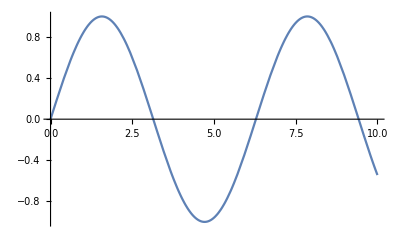
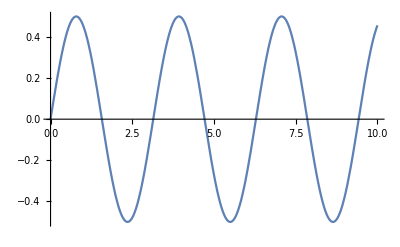
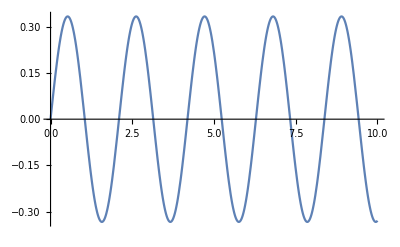
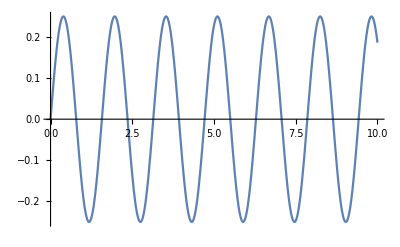
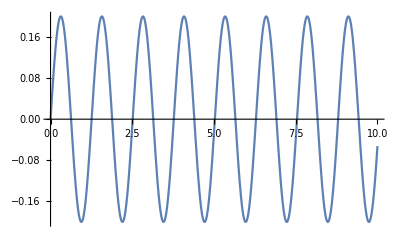
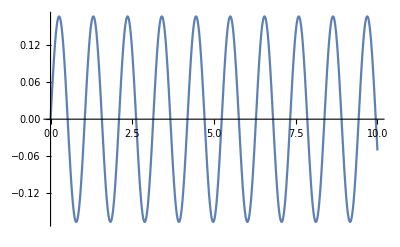
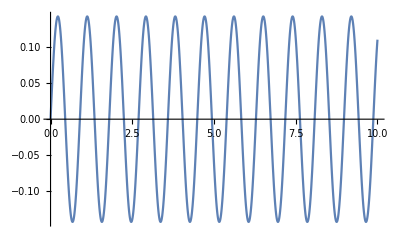
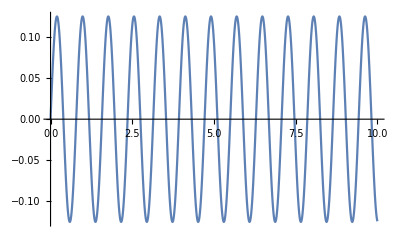

```mathematica
Table[ϕ[x]/.NDSolve[{ϕ''[x]+ω^2 ϕ[x]==0, ϕ[0]==0,ϕ'[0]==1},ϕ[x],{x,0,10}],{ω,10}];
Table[Plot[%⟦i⟧,{x,0,10}],{i,Length[%]}]
Plot[%%,{x,0,10},PlotRange->Full]
```

### Numerical solution with damping

For a fixed value of frequency, this part shows the solution for the different value of the damping constant. 

Animation here again

```mathematica
sol=Table[ϕ[x]/.NDSolve[{ϕ''[x]+γ/10 ϕ'[x]+10^2 ϕ[x]==0, ϕ[0]==0,ϕ'[0]==1},ϕ[x],{x,0,10}],{γ,0,10}];
```

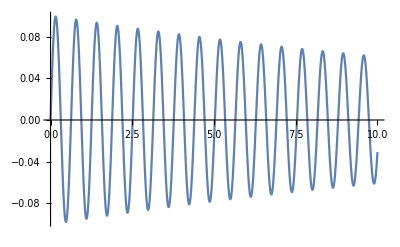
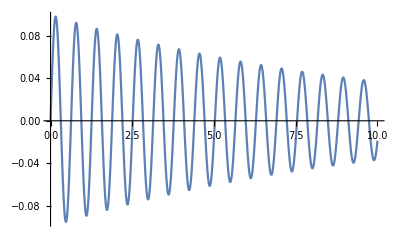
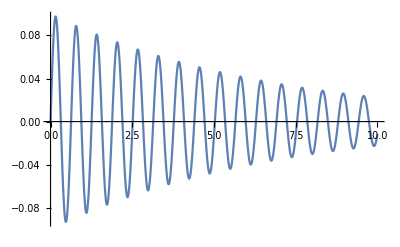
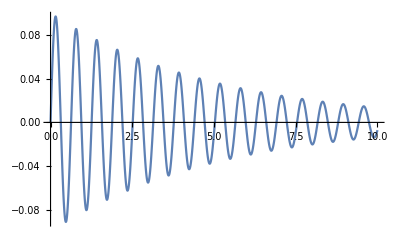
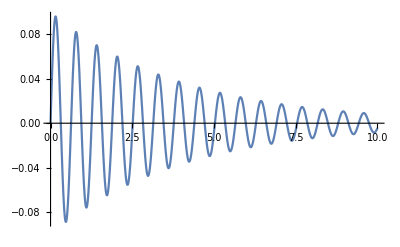
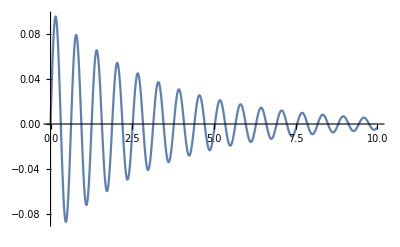
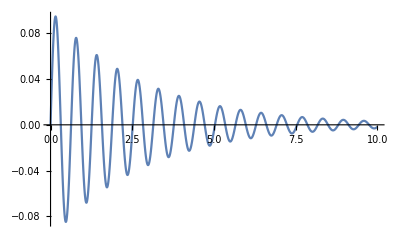
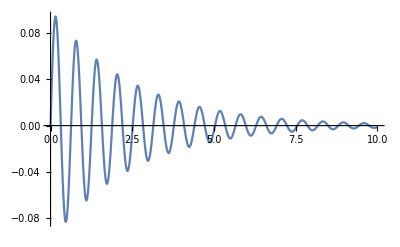
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

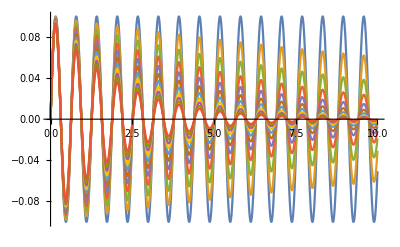

```mathematica
Table[Plot[sol⟦i⟧,{x,0,10},PlotRange->Full],{i,Length[sol]}]
Plot[sol,{x,0,10}]
```

### Forced oscillator

This is the effect of the external driving force.

```mathematica
sol=Table[ϕ[x]/.NDSolve[{ϕ''[x]+10^2 ϕ[x]==Sin[i x], ϕ[0]==0,ϕ'[0]==1},ϕ[x],{x,0,10}],{i,0,10}];
```

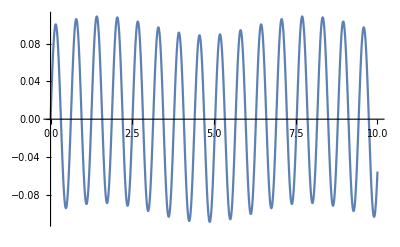
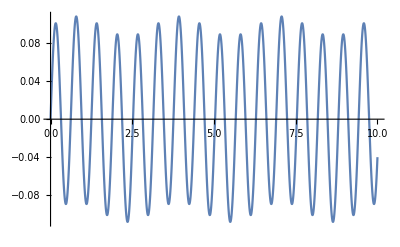
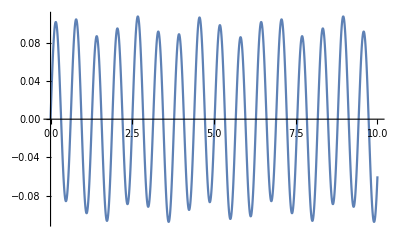
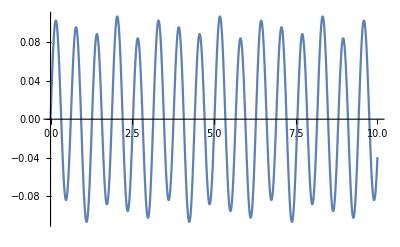
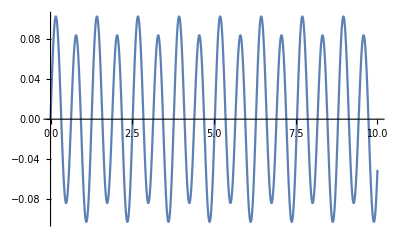
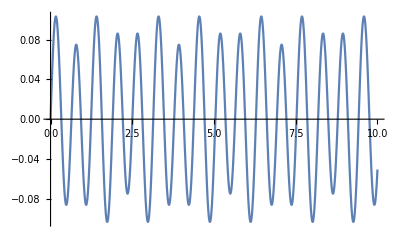
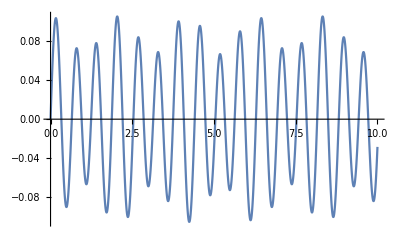
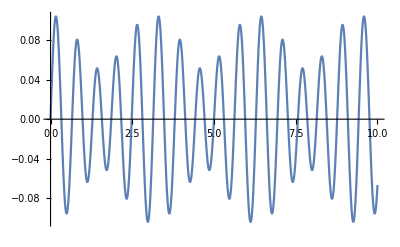
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

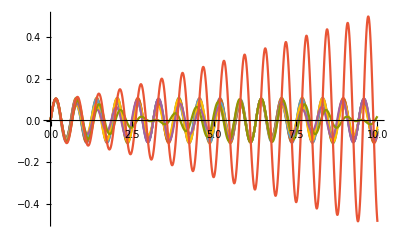

```mathematica
solplotlist=Table[Plot[sol⟦i⟧,{x,0,10},PlotRange->Full],{i,Length[sol]}]
Plot[sol,{x,0,10},PlotRange->Full]
```